Autor: Krzysztof Barczak

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 7

Metoda różnic skończonych

Napisać procedurę realizującą metodę różnic skończonych dla zagadnienia brzegowego liniowego równania różniczkowego zwyczajnego rzędu drugiego. Działanie procedury przetestować na przykładzie podanym na wykładzie.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia brzegowego:

{m y''(x)+ k y'(x) +s y(x)=0,  x∈[0,10],
y(0)=1, y(10)=1,

Obliczenia wykonać dla dwóch zestawów danych:
a) m=1, k=3, s=2;
b) m=5, k=2, s=10.

Za każdym razem obliczenia wykonać dla 500 i 1000 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Policzyć ponadto błędy maksymalne oraz średnie dla obu siatek oraz zestawić je na wykresie słupkowym, np. postaci:

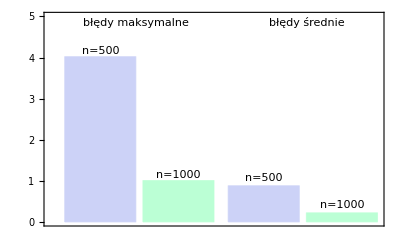

## Rozwiązanie

### Kod procedury

Procedura znajduje rozwiązanie równania postaci:
	
z warunkami brzegowymi:
	
	.
metodą różnic skończonych.

Wejście:
	AA, BB, CC, DD - współczynniki równania;
	a, b - rozważany przedział;
	α1, α2, β1, β2, za, zb - współczynniki z warunków brzegowych;
	n - liczba naturalna.
Wyjście:
	Wektor {(x_0,y_0),(x_1,y_1), ..., (x_n,y_n)}.

```mathematica
Clear[mrs];
mrs[AA_,BB_,CC_,DD_,a_,b_,α1_,α2_,β1_,β2_,za_,zb_,n_]:=Module[{h=(b-a)/n,xi,Ai,Bi,Ci,Di,macierz,pierwszy,ostatni,wolne,y},

xi=Table[a+i h,{i,0,n}];
(*Print["xi ",xi];*)

macierz=Table[i,j+1(2AA[xi[[i]]]-h BB[xi[[i]]])+i,j(2(h^2) CC[xi[[i]]]-4 AA[xi[[i]]])+i,j-1(2AA[xi[[i]]]+h BB[xi[[i]]]),{i,2,n},{j,n+1}];
(*Print[MatrixForm[macierz]];*)

pierwszy=Table[i,1(2h α1-3α2)+i,2(4α2)+i,3(-α2),{i,n+1}];
(*Print["pierwszy ",pierwszy];*)

ostatni=Table[i,n-1*β2+i,n*(-4β2)+i,n+1*(2h β1+3β2),{i,n+1}];
(*Print["ostatni ",ostatni];*)

macierz=Join[Join[{pierwszy},macierz,1],{ostatni}];
(*Print[MatrixForm[macierz]];*)

wolne=Table[2h^2*DD[xi[[i]]],{i,2,n}];
wolne=Prepend[wolne,2h*za];
wolne=Append[wolne,2h*zb];
(*Print["wolne ",wolne];*)

y=LinearSolve[macierz,wolne];

Return[Transpose[{xi,y}]]

]
```

### Przykład wykładowy

```mathematica
Clear[AA,BB,CC,DD,a,b,α1,α2,β1,β2,za,zb,n];
AA[x_]:=x^2;BB[x_]:=-3x;CC[x_]:=5;DD[x_]:=x^2+5;a=0;b=4;α1=1;α2=1;β1=1;β2=1;za=1;zb=25;n=4;
mrs[AA,BB,CC,DD,a,b,α1,α2,β1,β2,za,zb,n]
```

{{0,1},{1,2},{2,5},{3,10},{4,17}}

### Zadanie

#### a)

```mathematica
Clear[AA,BB,CC,DD,a,b,α1,α2,β1,β2,za,zb,solution,h500,h1000,yDSolve500,bledy500,max500,mean500,yDSolve1000,bledy1000,max1000,mean1000,wykresDSolve,wykres500,wykres1000,wykresBledy500,wykresBledy1000];
AA[x_]:=1;BB[x_]:=3;CC[x_]:=2;DD[x_]:=0;a=0;b=10;α1=1;α2=0;β1=1;β2=0;za=1;zb=1;
sol500=mrs[AA,BB,CC,DD,a,b,α1,α2,β1,β2,za,zb,500];
sol1000=mrs[AA,BB,CC,DD,a,b,α1,α2,β1,β2,za,zb,1000];
```

```mathematica
solution=DSolve[{AA[x] y''[x]+BB[x] y'[x]+CC[x] y[x]==DD[x],α1 y[a]==za,β1 y[b]==zb},y[x],x][[1,1,2]]
```

ⅇ^(-2 x) (-ⅇ^10+ⅇ^x+ⅇ^(10+x))

```mathematica
h500=(b-a)/500;
yDSolve500=Table[solution/.{x->xw},{xw,a,a+500h500,h500}];
bledy500=Table[{sol500[[i,1]],Abs[sol500[[i,2]]-yDSolve500[[i]]]},{i,1,501}];
max500=N[Max[bledy500[[All,2]]]];
mean500=N[Mean[bledy500[[All,2]]]];
```

```mathematica
h1000=(b-a)/1000;
yDSolve1000=Table[solution/.{x->xw},{xw,a,a+1000h1000,h1000}];
bledy1000=Table[{sol1000[[i,1]],Abs[sol1000[[i,2]]-yDSolve1000[[i]]]},{i,1,1001}];
max1000=N[Max[bledy1000[[All,2]]]];
mean1000=N[Mean[bledy1000[[All,2]]]];
```

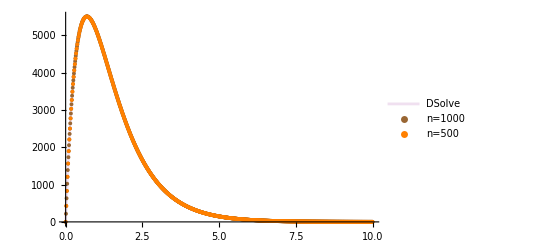

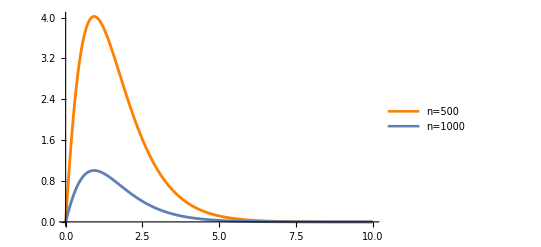

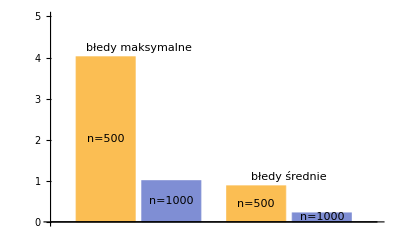

```mathematica
wykresDSolve=Plot[solution,{x,a,b},PlotLegends->{"DSolve"},PlotStyle->LightPurple];
wykres500=ListPlot[sol500,PlotStyle->Orange,PlotMarkers->{Automatic,Tiny},PlotLegends->{"n=500"}];
wykres1000=ListPlot[sol1000,PlotStyle->Brown,PlotMarkers->{Automatic,Tiny},PlotLegends->{"n=1000"}];

wykresBledy500=ListPlot[bledy500,Joined->True,PlotLegends->{"n=500"},PlotStyle->{Orange,Thickness[0.005]}];
wykresBledy1000=ListPlot[bledy1000,Joined->True,PlotLegends->{"n=1000"},PlotStyle->{Thickness[0.005]}];

Show[wykresDSolve,wykres1000,wykres500]
Show[wykresBledy500,wykresBledy1000]
BarChart[{{max500,max1000},{mean500,mean1000}},ChartLabels->{Placed[{"błedy maksymalne","błedy średnie"},Above],Placed[{"n=500","n=1000"},Center]},PlotRange->{0,5}]
```

#### b)

```mathematica
Clear[AA,BB,CC,DD,a,b,α1,α2,β1,β2,za,zb,solution,h500,h1000,yDSolve500,bledy500,max500,mean500,yDSolve1000,bledy1000,max1000,mean1000,wykresDSolve,wykres500,wykres1000,wykresBledy500,wykresBledy1000];
AA[x_]:=5;BB[x_]:=2;CC[x_]:=10;DD[x_]:=0;a=0;b=10;α1=1;α2=0;β1=1;β2=0;za=1;zb=1;
sol500=mrs[AA,BB,CC,DD,a,b,α1,α2,β1,β2,za,zb,500];
sol1000=mrs[AA,BB,CC,DD,a,b,α1,α2,β1,β2,za,zb,1000];
```

```mathematica
solution=DSolve[{AA[x] y''[x]+BB[x] y'[x]+CC[x] y[x]==DD[x],α1 y[a]==za,β1 y[b]==zb},y[x],x][[1,1,2]]
```

ⅇ^(-x/5) (Cos[(7 x)/5]-Cot[14] Sin[(7 x)/5]+ⅇ^2 Csc[14] Sin[(7 x)/5])

```mathematica
h500=(b-a)/500;
yDSolve500=Table[solution/.{x->xw},{xw,a,a+500h500,h500}];
bledy500=Table[{sol500[[i,1]],Abs[sol500[[i,2]]-yDSolve500[[i]]]},{i,1,501}];
max500=N[Max[bledy500[[All,2]]]];
mean500=N[Mean[bledy500[[All,2]]]];
```

```mathematica
h1000=(b-a)/1000;
yDSolve1000=Table[solution/.{x->xw},{xw,a,a+1000h1000,h1000}];
bledy1000=Table[{sol1000[[i,1]],Abs[sol1000[[i,2]]-yDSolve1000[[i]]]},{i,1,1001}];
max1000=N[Max[bledy1000[[All,2]]]];
mean1000=N[Mean[bledy1000[[All,2]]]];
```

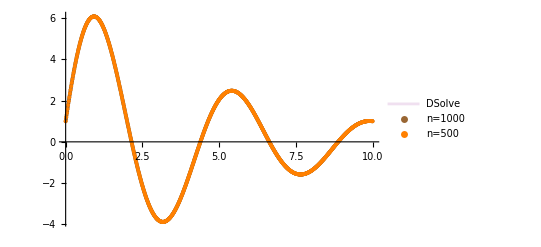

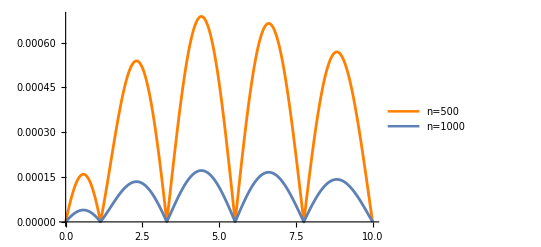

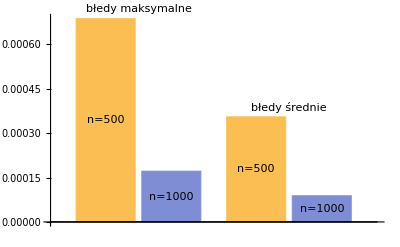

```mathematica
wykresDSolve=Plot[solution,{x,a,b},PlotLegends->{"DSolve"},PlotStyle->LightPurple];
wykres500=ListPlot[sol500,PlotStyle->Orange,PlotMarkers->{Automatic,Tiny},PlotLegends->{"n=500"}];
wykres1000=ListPlot[sol1000,PlotStyle->Brown,PlotMarkers->{Automatic,Tiny},PlotLegends->{"n=1000"}];

wykresBledy500=ListPlot[bledy500,Joined->True,PlotLegends->{"n=500"},PlotStyle->{Orange,Thickness[0.005]}];
wykresBledy1000=ListPlot[bledy1000,Joined->True,PlotLegends->{"n=1000"},PlotStyle->{Thickness[0.005]}];

Show[wykresDSolve,wykres1000,wykres500]
Show[wykresBledy500,wykresBledy1000]
BarChart[{{max500,max1000},{mean500,mean1000}},ChartLabels->{Placed[{"błedy maksymalne","błedy średnie"},Above],Placed[{"n=500","n=1000"},Center]}]
```